```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
(****************************************)
```

```mathematica
dateMouseSessionListV1toV2m={{"082120","Mouse21060","Session2"},{"082220","Mouse21060","Session3"},{"082320","Mouse21060","Session2"},{"082520","Mouse21060","Session2"},{"090620","Mouse21060","Session1"},{"090820","Mouse21067","Session2"},{"101720","Mouse23392","Session1"},{"101520","Mouse23393","Session2"},{"101420","Mouse23395","Session2"},{"121020","Mouse23379","Session1"},{"121520","Mouse23365","Session2"},{"122020","Mouse23365","Session1"},{"121520","Mouse23379","Session2"},{"121920","Mouse23379","Session1"},{"020421","Mouse23320","Session1"},{"020421","Mouse23329","Session1"},{"022721","Mouse23329","Session1"},{"030621","Mouse23329","Session1"},{"071721","Mouse21108","Session1"}};
```

```mathematica
dateMouseSessionListLPtoV2m={{"102020","Mouse23394","Session2"},{"102320","Mouse23394","Session1"},{"100720","Mouse23399","Session2"},{"101020","Mouse23399","Session2"},{"110120","Mouse23394","Session2"},{"103120","Mouse23378","Session2"},{"110320","Mouse23378","Session1"},{"110120","Mouse23377","Session1"},{"111620","Mouse23384","Session1"},{"111720","Mouse23384","Session3"},{"112020","Mouse23384","Session2"},{"120420","Mouse23378","Session1"},{"120220","Mouse23378","Session2"},{"120420","Mouse23384","Session1"},{"120220","Mouse23384","Session2"},{"121620","Mouse23381","Session2"},{"121920","Mouse23381","Session1"},{"011221","Mouse23369","Session1"},{"011521","Mouse23369","Session2"},{"010721","Mouse23339","Session1"},{"011521","Mouse23339","Session1"},{"030921","Mouse23339","Session1"},{"031121","Mouse23369","Session1"},{"070122","Mouse23067","Session1"},{"071122","Mouse23075","Session1"}};
```

```mathematica
dateMouseSessionListLMtoV2m={{"092221","Mouse22422","Session1"},{"100421","Mouse22422","Session1"},{"081221","Mouse22437","Session2"},{"081521","Mouse22437","Session1"},{"082021","Mouse22437","Session1"},{"082421","Mouse22437","Session1"},{"092321","Mouse22472","Session1"},{"101021","Mouse22472","Session1"},{"081921","Mouse22491","Session1"},{"102021","Mouse22422","Session1"},{"102121","Mouse22436","Session1"},{"102221","Mouse22472","Session1"},{"071522","Mouse23025","Session1"},{"071222","Mouse23100","Session2"},{"071122","Mouse23014","Session1"},{"070822","Mouse22518","Session1"},{"071022","Mouse22518","Session1"}};
```

```mathematica
(***Preferred spatial frequency***)
```

```mathematica
prefSFsV1toV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/V1toV2m/ValuesForPlotting/prefSFs_V1toV2m_nonDupROIs.txt","List"]];
```

```mathematica
prefSFsLPtoV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LPtoV2m/ValuesForPlotting/prefSFs_LPtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
prefSFsLMtoV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LMtoV2m/ValuesForPlotting/prefSFs_LMtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
v1AxonCharts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSFsV1toV2m]}],prefSFsV1toV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0.01,0.33}},Axes->False],BoxWhiskerChart[prefSFsV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSFsV1toV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0.01,0.34,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSFsLMtoV2m]}],prefSFsLMtoV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0.01,0.33}},Axes->False],BoxWhiskerChart[prefSFsLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSFsLMtoV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0.01,0.34,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSFsLPtoV2m]}],prefSFsLPtoV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0.01,0.33}},Axes->False],BoxWhiskerChart[prefSFsLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSFsLPtoV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0.01,0.34,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSFsLPtoV2m]}],prefSFsLPtoV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0.01,0.33}},FrameTicks->{{LinTicks[0.01,0.34,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],BoxWhiskerChart[prefSFsLPtoV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},ChartStyle->Transparent,Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSFsLPtoV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False,ScalingFunctions->"Log"]];
```

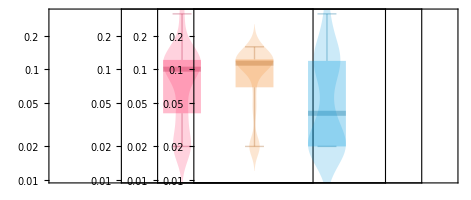

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-400}}]
```

```mathematica
(***Preferred speed***)
```

```mathematica
prefSpeedsV1toV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/V1toV2m/ValuesForPlotting/prefSpeeds_V1toV2m_nonDupROIs.txt","List"]];
```

```mathematica
prefSpeedsLPtoV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LPtoV2m/ValuesForPlotting/prefSpeeds_LPtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
prefSpeedsLMtoV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LMtoV2m/ValuesForPlotting/prefSpeeds_LMtoV2m_nonDupROIs.txt","List"]];
```

```mathematica
v1AxonCharts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSpeedsV1toV2m]}],prefSpeedsV1toV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0,1500}},Axes->False],BoxWhiskerChart[prefSpeedsV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSpeedsV1toV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0,1500,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSpeedsLMtoV2m]}],prefSpeedsLMtoV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0,1500}},Axes->False],BoxWhiskerChart[prefSpeedsLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSpeedsLMtoV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0,1500,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSpeedsLPtoV2m]}],prefSpeedsLPtoV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0,1500}},Axes->False],BoxWhiskerChart[prefSpeedsLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSpeedsLPtoV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0,1500,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSpeedsLPtoV2m]}],prefSpeedsLPtoV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0,1500}},FrameTicks->{{LinTicks[0,1500,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLogPlot[Partition[Partition[Riffle[Table[-0.6,{Length[Range[5,720,55]]}],Range[5,720,55]],2],1],PlotStyle->Black,PlotRange->{{-0.63,2},{0,1500}},Axes->False],BoxWhiskerChart[prefSpeedsLPtoV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},ChartStyle->Transparent,Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSpeedsLPtoV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False,ScalingFunctions->"Log"]];
```

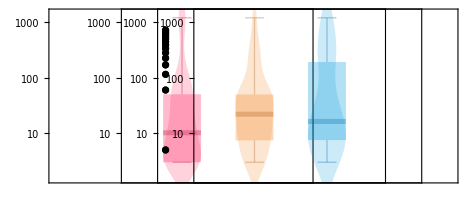

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-400}}]
```